```mathematica
(*This file just goes about finding various properties of a typical image*)
```

```mathematica
(*we use the side view of the stanford bunny. We only use the red channel (hence ⟦All,All,1⟧), since it is in greyscale.*) pic=ImageData[-Graphics-]⟦All,All,1⟧;
```

```mathematica
(*this counts the number of not zero pixels*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0,
n++]]];
n
```

98209

```mathematica
(*number of pixels after removing isolated pixles (pixels surronded by zeros)*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,
n++]]];
n
```

98209

```mathematica
(*Here we count the number of high and low points. Since edges have zeros next to them, zero pixels are set to 1 in order to find the low points*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧>Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧}]||pic⟦x,y⟧<Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}],n++]]]]
n
```

1582

```mathematica
(*number of high points and low points which are removed from the surface. This calculation takes a long time*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧>Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255||pic⟦x,y⟧<Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,n++]]]]
n
```

61

```mathematica
(*number of points after wayward peaks are removed*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,n++]]]]
n
```

98148

```mathematica
(*number of points after wayward peaks are removed, which have any curvature (tracked by n) or gradient (tracked by m)*)
For[x=2;n=0;m=0;s=7/255,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,If[Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]≥s,n++];If[(Abs[pic⟦x+1,y⟧-pic⟦x-1,y⟧]+Abs[pic⟦x,y+1⟧-pic⟦x,y-1⟧]≥ s),m++]]]]]
{n,m}
```

{2643,3974}

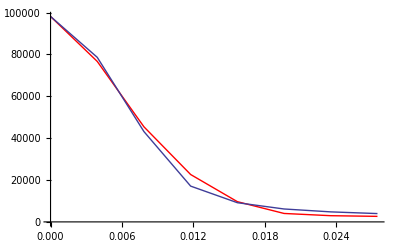

```mathematica
(*The following graph shows the number of points kept as a function of the sensitivity to curvature (red) and gradient (blue) (after wayward points are removed)*)
Show[ListPlot[{{0,98148},{1/255,76665},{2/255,45425},{3/255,22634},{4/255,9664},{5/255,4030},{6/255,2961},{7/255,2643}},Joined->True,PlotStyle->Red],ListPlot[{{0,98148},{1/255,78626},{2/255,43145},{3/255,17094},{4/255,9170},{5/255,6169},{6/255,4786},{7/255,3974}},Joined->True]]
```

```mathematica
(*Reconstructing the image after removing the points which are removed from the surface. *)
For[x=2;rec1={},x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧<Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧}]+2/255&&pic⟦x,y⟧>Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,rec1=Append[rec1,{x,y,pic⟦x,y⟧}]]]]]
(*This interpolation function only allows for linear interpolation on an irregular grid*) Interpolation[Table[{{rec1⟦i,1⟧,rec1⟦i,2⟧},rec1⟦i,3⟧},{i,1,Length[rec1]}]]
(*Here the ceiling is used to get rid of the noise values beyond the edges of the image. The image can be reconstructed without it*) 
pic1=Table[Ceiling[pic⟦X,Y⟧]*%[X,Y],{X,1,480},{Y,1,640}];
{Image[pic],Image[pic1]}
(*In order to find some sort of measure of how accurate our reconstruction is, we simply find the total of the original image less the total of the reconstructed image*)
Total[Abs[pic-pic1],2]
```

InterpolatingFunction[{{33.,430.},{111.,512.}},<>]

{-Graphics-,-Graphics-}

3.54657

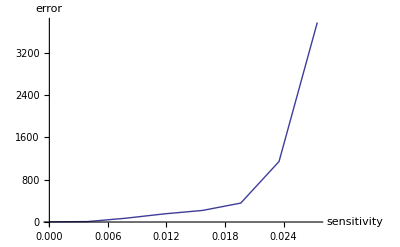

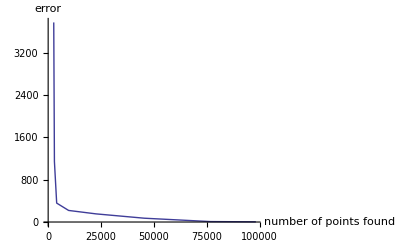

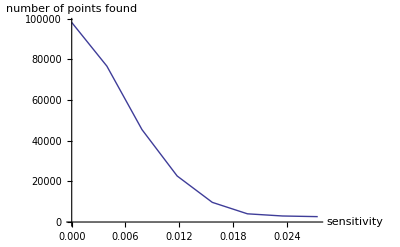

```mathematica
(*accuracy of the reconstruction as a function of the sensitivity to curvature*)
ListPlot[{{0,3.54657},{1/255,8.2784},{2/255,71.9164},{3/255,153.662},{4/255,218.599},{5/255,357.425},{6/255,1142.95},{7/255,3770.08}},Joined->True,AxesLabel->{"sensitivity","error"}]
(*One can also plot the error as a function of the number of points we choose to retain.*)
ListPlot[{{98148,3.54657},{76665,8.2784},{45425,71.9164},{22634,153.662},{9664,218.599},{4030,357.425},{2961,1142.95},{2643,3770.08}},Joined->True,AxesLabel->{"number of points found","error"}]
(*As already plotted, the number of points retained as a function of the curvature*)
ListPlot[{{0,98148},{1/255,76665},{2/255,45425},{3/255,22634},{4/255,9664},{5/255,4030},{6/255,2961},{7/255,2643}},Joined->True,AxesLabel->{"sensitivity","number of points found"}]
```

```mathematica
(*Reconstructing the image after removing the points which are removed from the surface. *)
For[x=2;rec2={};s=5/255,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0, If[Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]≥s,If[Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧<Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧}]+2/255&&pic⟦x,y⟧>Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}] - 2/255,rec2=Append[rec2,{x,y,pic⟦x,y⟧}]]]]]]]
(*This interpolation function only allows for linear interpolation on an irregular grid*) Interpolation[Table[{{rec2⟦i,1⟧,rec2⟦i,2⟧},rec2⟦i,3⟧},{i,1,Length[rec2]}]]
pic2=Table[Ceiling[pic⟦X,Y⟧]*%[X,Y],{X,1,480},{Y,1,640}];
(*The first image is the original picture, the second is the reconstrruction, and th third shows where the differences between the two images occur*)
{Image[pic],Image[pic2],Image[50*Abs[pic2-pic]]}
(*In order to find some sort of measure of how accurate our reconstruction is, we simply find the total of the original image less the total of the reconstructed image*)
Total[Abs[pic-pic2],2]
```

InterpolatingFunction[{{33.,430.},{111.,512.}},<>]

{-Graphics-,-Graphics-,-Graphics-}

357.425